```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"sampler3`";
```

```mathematica
ρ=1-10^-15;
SIGMA={{1,ρ},{ρ,1}};
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
Uq[x_,y_]=D1[U[x,y],{x,y}];
Uqq[x_,y_]=D2[U[x,y],{x,y}];
```

```mathematica
Dim=2;
BURNIN=5000;
ITERATIONS=10000;
```

```mathematica
QS=hmc[U,Uq,Uqq,Dim,BURNIN,ITERATIONS,{}];
```

100118.4406×10^62.714690.3573160.3653424.67969{1,3,6}{3,5,6}0.0001685358.4406×10^60.000168535FalseFalse

200224.1376×10^122.133610.476280.1924710.726563{1}{6}2.34744×10^-74.1376×10^122.34744×10^-7FalseFalse

300311.06216×10^171.988780.4366620.4888361.01611{1,4}{1,6}1.81789×10^-91.06216×10^171.81789×10^-9FalseFalse

400421.1161×10^233.904420.64280.3174012.50391{1,3}{6}1.42928×10^-121.1161×10^231.42928×10^-12FalseFalse

500512.82208×10^281.250280.2380970.08817942.67957{1,4}{1,6}3.20616×10^-152.82208×10^283.20616×10^-15TrueFalse

600622.90784×10^290.2456820.4846730.4801153.12891{1,4}{1,6}7.67528×10^-162.90784×10^297.67528×10^-16TrueFalse

700712.82208×10^282.4720.6692990.3460083.70313{1,4}{1,6}3.20616×10^-152.82208×10^283.20616×10^-15TrueFalse

800822.90784×10^291.308850.5930660.3624312.47656{1,4}{1,6}7.67528×10^-162.90784×10^297.67528×10^-16TrueFalse

900912.82208×10^281.914430.6177690.07780432.03882{1,4}{1,6}3.20616×10^-152.82208×10^283.20616×10^-15TrueFalse

{1.00475,1.03162}

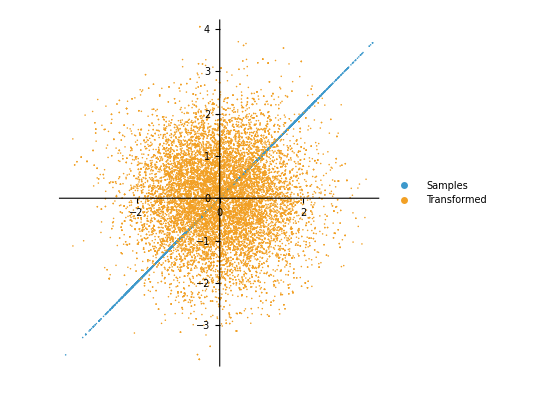

```mathematica
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[{QS,QS1},PlotStyle->Opacity[1],AspectRatio->1,PlotLegends->{Samples, Transformed}]
```

```mathematica
psrf[QS]
```

{1.00005,1.00005}